### Initialize

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

### Half diagrams

```mathematica
SetOptions[GV,Dimension->4,Explicit->True]
SetOptions[SUNSimplify,Explicit->True,SUNNToCACF->False]
```

{CouplingConstant→g_s,Dimension→4,Explicit→True,Ω→False}

{Expanding→False,Explicit→True,Factoring→False,SUNIndexRename→True,SUNFJacobi→False,SUNNToCACF→False,SUNTrace→False}

```mathematica
polSum:= PolarizationSum[μ1,μ2,p2+p3-p1,η] PolarizationSum[ν1,ν2,p1,η]  PolarizationSum[ρ1,ρ2,p2,η] PolarizationSum[σ1,σ2,p3,η]
```

```mathematica
amp[p_,μ_,a_,p1_,α_,a1_,p2_,β_,a2_,p3_,γ_,a3_]:=Module[{σ,σb,b1,pu,p1u,p2u,p3u},
pu={p,μ,a};p1u={p1,α,a1};p2u={-p2,β,a2};p3u={-p3,γ,a3};
{ GV[pu,p1u,p2u,p3u] ,GV[pu,p1u,{-p-p1,σ,b1}] -I/s GV[{p+p1,σ,b1},p2u,p3u],GV[pu,p2u,{-p+p2,σ,b1}] -I/t GV[{p-p2,σ,b1},p1u,p3u],GV[pu,p3u,{-p+p3,σ,b1}] -I/u GV[{p-p3,σ,b1},p1u,p2u]}
]
```

```mathematica
diagR=amp[p2+p3-p1,μ1,a,p1,ν1,b,p2,ρ1,c,p3,σ1,d];
diagL=amp[p2,ρ2,c,p3,σ2,d,p2+p3-p1,μ2,a,p1,ν2,b];
```

```mathematica
ScalarProduct[η,η]=0;ScalarProduct[p1,p1]=0;ScalarProduct[p2,p2]=0;ScalarProduct[p3,p3]=0;
ScalarProduct[p2+p3-p1,p2+p3-p1]=0;
ScalarProduct[p2,p3]=-u/2-t/2;ScalarProduct[p1,p3]=-t/2;ScalarProduct[p1,p2]=-u/2;
```

#### test run

```mathematica
Msqgggg=0;
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
ms=Timing[FullSimplify[
SUNSimplify[ Contract[diagR[[i]] diagL[[j]] polSum]]]];
Print[i,",",j," = ",ms];Msqgggg+=ms;
]
]
```

1,1 = {9.024,-18 N^2 (N^2-1) g_s^4}

1,2 = {14.832,(3 N^2 (N^2-1) (2 (OverBar[p1]·η̄)-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p2]·η̄-OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄) (OverBar[p2]·η̄-OverBar[p3]·η̄)-(OverBar[p2]·η̄+OverBar[p3]·η̄) (t (OverBar[p2]·η̄)-u (OverBar[p3]·η̄))) g_s^4)/(s (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))}

1,3 = {15.108,-(3 N^2 (N^2-1) (OverBar[p1]·η̄-2 (OverBar[p2]·η̄)-OverBar[p3]·η̄) (OverBar[p1]·η̄+OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄)^2-(t (OverBar[p2]·η̄)+(t+2 u) (OverBar[p3]·η̄)) (OverBar[p1]·η̄)+(OverBar[p3]·η̄) (u (OverBar[p3]·η̄)-t (OverBar[p2]·η̄))) g_s^4)/(t (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))}

1,4 = {15.008,-(3 N^2 (N^2-1) (OverBar[p1]·η̄+OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-2 (OverBar[p3]·η̄)) ((OverBar[p1]·η̄-OverBar[p2]·η̄) ((t+u) (OverBar[p1]·η̄)-t (OverBar[p2]·η̄))-u (OverBar[p1]·η̄+OverBar[p2]·η̄) (OverBar[p3]·η̄)) g_s^4)/(u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))}

2,1 = {15.08,(3 N^2 (N^2-1) (2 (OverBar[p1]·η̄)-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p2]·η̄-OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄) (OverBar[p2]·η̄-OverBar[p3]·η̄)-(OverBar[p2]·η̄+OverBar[p3]·η̄) (t (OverBar[p2]·η̄)-u (OverBar[p3]·η̄))) g_s^4)/(s (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))}

2,2 = {30.116,1/(s^2 (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))4 N^2 (N^2-1) (4 (t+u)^2 (OverBar[p1]·η̄)^4-2 (t+u) ((3 t+5 u) (OverBar[p2]·η̄)+(5 t+3 u) (OverBar[p3]·η̄)) (OverBar[p1]·η̄)^3+(2 (t+u) (7 t+10 u) (OverBar[p2]·η̄)^2+(17 t^2+38 u t+17 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+2 (t+u) (10 t+7 u) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+(-(t+u) (11 t+15 u) (OverBar[p2]·η̄)^3-2 (11 t^2+24 u t+11 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2-2 (11 t^2+24 u t+11 u^2) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)-(t+u) (15 t+11 u) (OverBar[p3]·η̄)^3) (OverBar[p1]·η̄)+(t+u) ((7 t+8 u) (OverBar[p2]·η̄)^4+17 (t+u) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+23 (t+u) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)^2+17 (t+u) (OverBar[p3]·η̄)^3 (OverBar[p2]·η̄)+(8 t+7 u) (OverBar[p3]·η̄)^4)) g_s^4}

2,3 = {28.292,1/(s t (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))N^2 (N^2-1) (2 (5 t-u) (t+u) (OverBar[p1]·η̄)^4+((-11 t^2-7 u t+8 u^2) (OverBar[p2]·η̄)-t (29 t+25 u) (OverBar[p3]·η̄)) (OverBar[p1]·η̄)^3+((18 t^2+18 u t-7 u^2) (OverBar[p2]·η̄)^2+4 (12 t^2+11 u t-2 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+5 (9 t^2+9 u t+u^2) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+((-11 t^2-15 u t+4 u^2) (OverBar[p2]·η̄)^3+4 (-12 t^2-13 u t+u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+(-51 t^2-51 u t+2 u^2) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)-2 (4 t+u) (4 t+3 u) (OverBar[p3]·η̄)^3) (OverBar[p1]·η̄)+2 t (5 t+6 u) (OverBar[p2]·η̄)^4+(4 t+u) (4 t+3 u) (OverBar[p3]·η̄)^4+2 (4 t+u) (4 t+3 u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+5 (9 t^2+9 u t+u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+(t+u) (29 t+4 u) (OverBar[p2]·η̄)^3 (OverBar[p3]·η̄)) g_s^4}

2,4 = {28.756,1/(s u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))N^2 (N^2-1) (-2 (t-5 u) (t+u) (OverBar[p1]·η̄)^4+((8 t^2-7 u t-11 u^2) (OverBar[p3]·η̄)-u (25 t+29 u) (OverBar[p2]·η̄)) (OverBar[p1]·η̄)^3+(5 (t^2+9 u t+9 u^2) (OverBar[p2]·η̄)^2+4 (-2 t^2+11 u t+12 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+(-7 t^2+18 u t+18 u^2) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+(-2 (t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^3+(2 t^2-51 u t-51 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+4 (t^2-13 u t-12 u^2) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)+(4 t^2-15 u t-11 u^2) (OverBar[p3]·η̄)^3) (OverBar[p1]·η̄)+(t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^4+2 u (6 t+5 u) (OverBar[p3]·η̄)^4+(t+u) (4 t+29 u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+5 (t^2+9 u t+9 u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+2 (t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^3 (OverBar[p3]·η̄)) g_s^4}

3,1 = {15.028,-(3 N^2 (N^2-1) (OverBar[p1]·η̄-2 (OverBar[p2]·η̄)-OverBar[p3]·η̄) (OverBar[p1]·η̄+OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄)^2-(t (OverBar[p2]·η̄)+(t+2 u) (OverBar[p3]·η̄)) (OverBar[p1]·η̄)+(OverBar[p3]·η̄) (u (OverBar[p3]·η̄)-t (OverBar[p2]·η̄))) g_s^4)/(t (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))}

3,2 = {28.004,1/(s t (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))N^2 (N^2-1) (2 (5 t-u) (t+u) (OverBar[p1]·η̄)^4+((-11 t^2-7 u t+8 u^2) (OverBar[p2]·η̄)-t (29 t+25 u) (OverBar[p3]·η̄)) (OverBar[p1]·η̄)^3+((18 t^2+18 u t-7 u^2) (OverBar[p2]·η̄)^2+4 (12 t^2+11 u t-2 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+5 (9 t^2+9 u t+u^2) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+((-11 t^2-15 u t+4 u^2) (OverBar[p2]·η̄)^3+4 (-12 t^2-13 u t+u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+(-51 t^2-51 u t+2 u^2) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)-2 (4 t+u) (4 t+3 u) (OverBar[p3]·η̄)^3) (OverBar[p1]·η̄)+2 t (5 t+6 u) (OverBar[p2]·η̄)^4+(4 t+u) (4 t+3 u) (OverBar[p3]·η̄)^4+2 (4 t+u) (4 t+3 u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+5 (9 t^2+9 u t+u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+(t+u) (29 t+4 u) (OverBar[p2]·η̄)^3 (OverBar[p3]·η̄)) g_s^4}

3,3 = {27.652,1/(t^2 (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))4 N^2 (N^2-1) (t (7 t-u) (OverBar[p1]·η̄)^4+t ((4 u-11 t) (OverBar[p2]·η̄)-17 t (OverBar[p3]·η̄)) (OverBar[p1]·η̄)^3+(2 t (7 t-3 u) (OverBar[p2]·η̄)^2+2 (11 t^2-2 u t-2 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+23 t^2 (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+(2 t (2 u-3 t) (OverBar[p2]·η̄)^3+(-17 t^2+4 u t+4 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+2 (-11 t^2+2 u t+2 u^2) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)-17 t^2 (OverBar[p3]·η̄)^3) (OverBar[p1]·η̄)+t (4 t (OverBar[p2]·η̄)^4+2 (5 t+2 u) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+2 (10 t+3 u) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)^2+(15 t+4 u) (OverBar[p3]·η̄)^3 (OverBar[p2]·η̄)+(8 t+u) (OverBar[p3]·η̄)^4)) g_s^4}

3,4 = {38.052,1/(t u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))N^2 (N^2-1) ((t-3 u) (3 t-u) (OverBar[p1]·η̄)^4-2 (t-3 u) (3 t-u) (OverBar[p2]·η̄+OverBar[p3]·η̄) (OverBar[p1]·η̄)^3+(5 (t^2-7 u t+u^2) (OverBar[p2]·η̄)^2-(2 t^2+55 u t+2 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+5 (t^2-7 u t+u^2) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+(OverBar[p2]·η̄+OverBar[p3]·η̄) ((25 t-4 u) u (OverBar[p2]·η̄)^2+(8 t^2+35 u t+8 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+t (25 u-4 t) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)-2 t (t+6 u) (OverBar[p2]·η̄)^4-2 u (6 t+u) (OverBar[p3]·η̄)^4-(4 t^2+23 u t+8 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3-(7 t^2+32 u t+7 u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2-(8 t^2+23 u t+4 u^2) (OverBar[p2]·η̄)^3 (OverBar[p3]·η̄)) g_s^4}

4,1 = {15.248,-(3 N^2 (N^2-1) (OverBar[p1]·η̄+OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-2 (OverBar[p3]·η̄)) ((OverBar[p1]·η̄-OverBar[p2]·η̄) ((t+u) (OverBar[p1]·η̄)-t (OverBar[p2]·η̄))-u (OverBar[p1]·η̄+OverBar[p2]·η̄) (OverBar[p3]·η̄)) g_s^4)/(u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))}

4,2 = {28.192,1/(s u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))N^2 (N^2-1) (-2 (t-5 u) (t+u) (OverBar[p1]·η̄)^4+((8 t^2-7 u t-11 u^2) (OverBar[p3]·η̄)-u (25 t+29 u) (OverBar[p2]·η̄)) (OverBar[p1]·η̄)^3+(5 (t^2+9 u t+9 u^2) (OverBar[p2]·η̄)^2+4 (-2 t^2+11 u t+12 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+(-7 t^2+18 u t+18 u^2) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+(-2 (t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^3+(2 t^2-51 u t-51 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+4 (t^2-13 u t-12 u^2) (OverBar[p3]·η̄)^2 (OverBar[p2]·η̄)+(4 t^2-15 u t-11 u^2) (OverBar[p3]·η̄)^3) (OverBar[p1]·η̄)+(t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^4+2 u (6 t+5 u) (OverBar[p3]·η̄)^4+(t+u) (4 t+29 u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+5 (t^2+9 u t+9 u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+2 (t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^3 (OverBar[p3]·η̄)) g_s^4}

4,3 = {37.788,1/(t u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))N^2 (N^2-1) ((t-3 u) (3 t-u) (OverBar[p1]·η̄)^4-2 (t-3 u) (3 t-u) (OverBar[p2]·η̄+OverBar[p3]·η̄) (OverBar[p1]·η̄)^3+(5 (t^2-7 u t+u^2) (OverBar[p2]·η̄)^2-(2 t^2+55 u t+2 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+5 (t^2-7 u t+u^2) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)^2+(OverBar[p2]·η̄+OverBar[p3]·η̄) ((25 t-4 u) u (OverBar[p2]·η̄)^2+(8 t^2+35 u t+8 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)+t (25 u-4 t) (OverBar[p3]·η̄)^2) (OverBar[p1]·η̄)-2 t (t+6 u) (OverBar[p2]·η̄)^4-2 u (6 t+u) (OverBar[p3]·η̄)^4-(4 t^2+23 u t+8 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3-(7 t^2+32 u t+7 u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2-(8 t^2+23 u t+4 u^2) (OverBar[p2]·η̄)^3 (OverBar[p3]·η̄)) g_s^4}

4,4 = {28.204,1/(u^2 (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄) (OverBar[p3]·η̄))4 N^2 (N^2-1) (4 u^2 (OverBar[p3]·η̄)^4+2 u ((2 t-3 u) (OverBar[p1]·η̄)+(2 t+5 u) (OverBar[p2]·η̄)) (OverBar[p3]·η̄)^3+(2 u (7 u-3 t) (OverBar[p1]·η̄)^2+(4 t^2+4 u t-17 u^2) (OverBar[p2]·η̄) (OverBar[p1]·η̄)+2 u (3 t+10 u) (OverBar[p2]·η̄)^2) (OverBar[p3]·η̄)^2+((4 t-11 u) u (OverBar[p1]·η̄)^3-2 (2 t^2+2 u t-11 u^2) (OverBar[p2]·η̄) (OverBar[p1]·η̄)^2+2 (2 t^2+2 u t-11 u^2) (OverBar[p2]·η̄)^2 (OverBar[p1]·η̄)+u (4 t+15 u) (OverBar[p2]·η̄)^3) (OverBar[p3]·η̄)+u (-(t-7 u) (OverBar[p1]·η̄)^4-17 u (OverBar[p2]·η̄) (OverBar[p1]·η̄)^3+23 u (OverBar[p2]·η̄)^2 (OverBar[p1]·η̄)^2-17 u (OverBar[p2]·η̄)^3 (OverBar[p1]·η̄)+(t+8 u) (OverBar[p2]·η̄)^4)) g_s^4}

```mathematica
TrickMandelstam[Msqgggg,{s,t,u,0}]
```

{374.384,(16 N^2 (1-N^2) g_s^4 (t^2+t u+u^2)^3)/(s^2 t^2 u^2)}

## -iΠ_11

### Diag1

```mathematica
diag1=1/(2(CA^2-1))Contract[Explicit[diagR[[1]] diagL[[1]]]polSum]
```

1/(2 (C_A^2-1))(-4 g_s^4 f^(adFCGV(u24)) f^(adFCGV(u25)) f^(bcFCGV(u24)) f^(bcFCGV(u25))-2 g_s^4 f^(acFCGV(u24)) f^(adFCGV(u25)) f^(bcFCGV(u25)) f^(bdFCGV(u24))-2 g_s^4 f^(acFCGV(u25)) f^(adFCGV(u24)) f^(bcFCGV(u24)) f^(bdFCGV(u25))-4 g_s^4 f^(acFCGV(u24)) f^(acFCGV(u25)) f^(bdFCGV(u24)) f^(bdFCGV(u25))+2 g_s^4 f^(abFCGV(u24)) f^(adFCGV(u25)) f^(bcFCGV(u25)) f^(cdFCGV(u24))-2 g_s^4 f^(abFCGV(u24)) f^(acFCGV(u25)) f^(bdFCGV(u25)) f^(cdFCGV(u24))+2 g_s^4 f^(abFCGV(u25)) f^(adFCGV(u24)) f^(bcFCGV(u24)) f^(cdFCGV(u25))-2 g_s^4 f^(abFCGV(u25)) f^(acFCGV(u24)) f^(bdFCGV(u24)) f^(cdFCGV(u25))-4 g_s^4 f^(abFCGV(u24)) f^(abFCGV(u25)) f^(cdFCGV(u24)) f^(cdFCGV(u25)))

Here, Explicit -> True is very important.

```mathematica
diag1=FullSimplify[SUNSimplify[diag1]]
```

-9 N^2 g_s^4

### Diag2

```mathematica
FullSimplify[Contract[FourVector[p1+p2,α1] Explicit[GluonVertex[{p1+p2,α1,a},{p1,β1,b},{p2,γ2,c}]] Proj[β1,β2,p1]  Proj[γ1,γ2,p2] ]/.{ScalarProduct[η,η]->0,ScalarProduct[p1,p1]->0,ScalarProduct[p2,p2]->0}]
```

0

This just tells us that we can replace the intermediate propagator by that in Feynman gauge.

#### s channel

```mathematica
diag2s=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[diagR[[2]] diagL[[2]] polSum]]]
```

1/(s^2 (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))2 N^2 g_s^4 ((OverBar[p1]·η̄)^2 (2 (t+u) (7 t+10 u) (OverBar[p2]·η̄)^2+2 (t+u) (10 t+7 u) (OverBar[p3]·η̄)^2+(17 t^2+38 t u+17 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄))+(OverBar[p1]·η̄) (-2 (11 t^2+24 t u+11 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2-2 (11 t^2+24 t u+11 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^2-(t+u) (11 t+15 u) (OverBar[p2]·η̄)^3-(t+u) (15 t+11 u) (OverBar[p3]·η̄)^3)-2 (t+u) (OverBar[p1]·η̄)^3 ((3 t+5 u) (OverBar[p2]·η̄)+(5 t+3 u) (OverBar[p3]·η̄))+4 (t+u)^2 (OverBar[p1]·η̄)^4+(t+u) (17 (t+u) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+23 (t+u) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+17 (t+u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+(7 t+8 u) (OverBar[p2]·η̄)^4+(8 t+7 u) (OverBar[p3]·η̄)^4))

#### t channel

```mathematica
diag2t=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[diagR[[3]] diagL[[3]] polSum]]]
```

1/(t^2 (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))2 N^2 g_s^4 ((OverBar[p1]·η̄)^2 (2 t (7 t-3 u) (OverBar[p2]·η̄)^2+23 t^2 (OverBar[p3]·η̄)^2+2 (11 t^2-2 t u-2 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄))+(OverBar[p1]·η̄) ((-17 t^2+4 t u+4 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+2 (-11 t^2+2 t u+2 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^2+2 t (2 u-3 t) (OverBar[p2]·η̄)^3-17 t^2 (OverBar[p3]·η̄)^3)+t (OverBar[p1]·η̄)^3 ((4 u-11 t) (OverBar[p2]·η̄)-17 t (OverBar[p3]·η̄))+t (7 t-u) (OverBar[p1]·η̄)^4+t (2 (5 t+2 u) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+2 (10 t+3 u) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+(15 t+4 u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+4 t (OverBar[p2]·η̄)^4+(8 t+u) (OverBar[p3]·η̄)^4))

#### u channel

```mathematica
diag2u=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[diagR[[4]] diagL[[4]] polSum]]]
```

1/(u^2 (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))2 N^2 g_s^4 ((OverBar[p3]·η̄)^2 (2 u (7 u-3 t) (OverBar[p1]·η̄)^2+2 u (3 t+10 u) (OverBar[p2]·η̄)^2+(4 t^2+4 t u-17 u^2) (OverBar[p1]·η̄) (OverBar[p2]·η̄))+(OverBar[p3]·η̄) (-2 (2 t^2+2 t u-11 u^2) (OverBar[p2]·η̄) (OverBar[p1]·η̄)^2+2 (2 t^2+2 t u-11 u^2) (OverBar[p1]·η̄) (OverBar[p2]·η̄)^2+u (4 t-11 u) (OverBar[p1]·η̄)^3+u (4 t+15 u) (OverBar[p2]·η̄)^3)+2 u (OverBar[p3]·η̄)^3 ((2 t-3 u) (OverBar[p1]·η̄)+(2 t+5 u) (OverBar[p2]·η̄))+u (-17 u (OverBar[p2]·η̄) (OverBar[p1]·η̄)^3+23 u (OverBar[p1]·η̄)^2 (OverBar[p2]·η̄)^2-17 u (OverBar[p1]·η̄) (OverBar[p2]·η̄)^3-(t-7 u) (OverBar[p1]·η̄)^4+(t+8 u) (OverBar[p2]·η̄)^4)+4 u^2 (OverBar[p3]·η̄)^4)

```mathematica
diag2=FullSimplify[diag2u+diag2s+diag2t]
```

1/(s^2 t^2 u^2 (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))2 N^2 g_s^4 ((OverBar[p1]·η̄)^2 (t u^2 (s^2 (37 t-6 u)+2 t (t+u) (7 t+10 u)) (OverBar[p2]·η̄)^2+t^2 u (s^2 (37 u-6 t)+2 u (t+u) (10 t+7 u)) (OverBar[p3]·η̄)^2+(t^2 u^2 (17 t^2+38 t u+17 u^2)-4 s^2 (t^4+t^3 u-11 t^2 u^2+t u^3+u^4)) (OverBar[p2]·η̄) (OverBar[p3]·η̄))+(OverBar[p1]·η̄) ((s^2 (4 t^4+4 t^3 u-39 t^2 u^2+4 t u^3+4 u^4)-2 t^2 u^2 (11 t^2+24 t u+11 u^2)) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+(s^2 (4 t^4+4 t^3 u-39 t^2 u^2+4 t u^3+4 u^4)-2 t^2 u^2 (11 t^2+24 t u+11 u^2)) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^2-t u^2 (s^2 (23 t-4 u)+t (t+u) (11 t+15 u)) (OverBar[p2]·η̄)^3-t^2 u (s^2 (23 u-4 t)+u (t+u) (15 t+11 u)) (OverBar[p3]·η̄)^3)-2 t u (OverBar[p1]·η̄)^3 (u (2 s^2 (7 t-u)+t (t+u) (3 t+5 u)) (OverBar[p2]·η̄)+t (u (t+u) (5 t+3 u)-2 s^2 (t-7 u)) (OverBar[p3]·η̄))+t u (4 t u (t+u)^2-s^2 (t^2-14 t u+u^2)) (OverBar[p1]·η̄)^4+t u ((s^2 (4 t^2+25 t u+4 u^2)+17 t u (t+u)^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+(s^2 (6 t^2+40 t u+6 u^2)+23 t u (t+u)^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+(s^2 (4 t^2+25 t u+4 u^2)+17 t u (t+u)^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+t (s^2 (t+12 u)+u (t+u) (7 t+8 u)) (OverBar[p2]·η̄)^4+u (s^2 (12 t+u)+t (t+u) (8 t+7 u)) (OverBar[p3]·η̄)^4))

### Diag3

#### s - t channel

```mathematica
diag3st=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[2]] diagL[[3]]+diagR[[3]] diagL[[2]]) polSum]]]
```

1/(s t (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))N^2 g_s^4 ((OverBar[p1]·η̄)^3 ((-11 t^2-7 t u+8 u^2) (OverBar[p2]·η̄)-t (29 t+25 u) (OverBar[p3]·η̄))+(OverBar[p1]·η̄)^2 ((18 t^2+18 t u-7 u^2) (OverBar[p2]·η̄)^2+5 (9 t^2+9 t u+u^2) (OverBar[p3]·η̄)^2+4 (12 t^2+11 t u-2 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄))+(OverBar[p1]·η̄) (4 (-12 t^2-13 t u+u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+(-51 t^2-51 t u+2 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^2+(-11 t^2-15 t u+4 u^2) (OverBar[p2]·η̄)^3-2 (4 t+u) (4 t+3 u) (OverBar[p3]·η̄)^3)+2 (5 t-u) (t+u) (OverBar[p1]·η̄)^4+5 (9 t^2+9 t u+u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+2 (4 t+u) (4 t+3 u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+(t+u) (29 t+4 u) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+2 t (5 t+6 u) (OverBar[p2]·η̄)^4+(4 t+u) (4 t+3 u) (OverBar[p3]·η̄)^4)

#### s - u channel

```mathematica
diag3su=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[2]] diagL[[4]]+diagR[[4]] diagL[[2]]) polSum]]]
```

1/(s u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))N^2 g_s^4 ((OverBar[p1]·η̄)^3 ((8 t^2-7 t u-11 u^2) (OverBar[p3]·η̄)-u (25 t+29 u) (OverBar[p2]·η̄))+(OverBar[p1]·η̄)^2 (5 (t^2+9 t u+9 u^2) (OverBar[p2]·η̄)^2+(-7 t^2+18 t u+18 u^2) (OverBar[p3]·η̄)^2+4 (-2 t^2+11 t u+12 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄))+(OverBar[p1]·η̄) ((2 t^2-51 t u-51 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+4 (t^2-13 t u-12 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^2-2 (t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^3+(4 t^2-15 t u-11 u^2) (OverBar[p3]·η̄)^3)-2 (t-5 u) (t+u) (OverBar[p1]·η̄)^4+5 (t^2+9 t u+9 u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+(t+u) (4 t+29 u) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+2 (t+4 u) (3 t+4 u) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+(t+4 u) (3 t+4 u) (OverBar[p2]·η̄)^4+2 u (6 t+5 u) (OverBar[p3]·η̄)^4)

#### t - u channel

```mathematica
diag3tu=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[4]] diagL[[3]]+diagR[[3]] diagL[[4]]) polSum]]]
```

1/(t u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))N^2 g_s^4 ((OverBar[p1]·η̄)^2 (5 (t^2-7 t u+u^2) (OverBar[p2]·η̄)^2+5 (t^2-7 t u+u^2) (OverBar[p3]·η̄)^2-(2 t^2+55 t u+2 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄))+(OverBar[p1]·η̄) (OverBar[p2]·η̄+OverBar[p3]·η̄) (u (25 t-4 u) (OverBar[p2]·η̄)^2+t (25 u-4 t) (OverBar[p3]·η̄)^2+(8 t^2+35 t u+8 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄))-2 (t-3 u) (3 t-u) (OverBar[p2]·η̄+OverBar[p3]·η̄) (OverBar[p1]·η̄)^3+(t-3 u) (3 t-u) (OverBar[p1]·η̄)^4-(4 t^2+23 t u+8 u^2) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3-(7 t^2+32 t u+7 u^2) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2-(8 t^2+23 t u+4 u^2) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3-2 t (t+6 u) (OverBar[p2]·η̄)^4-2 u (6 t+u) (OverBar[p3]·η̄)^4)

```mathematica
diag3=FullSimplify[diag3st+diag3su+diag3tu]
```

1/(s t u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))N^2 g_s^4 (-2 (OverBar[p1]·η̄)^3 ((3 s t^2+3 u^2 (s+6 t)+2 t u (9 t-5 s)-4 u^3) (OverBar[p2]·η̄)+(t^2 (3 s-4 t)+3 u^2 (s+6 t)+2 t u (9 t-5 s)) (OverBar[p3]·η̄))+(OverBar[p1]·η̄)^2 ((5 t^2 (s+t)+u^2 (5 s+63 t)+7 t u (9 t-5 s)-7 u^3) (OverBar[p2]·η̄)^2+(5 s (t^2-7 t u+u^2)-7 t^3+63 t^2 u+63 t u^2+5 u^3) (OverBar[p3]·η̄)^2-(s (2 t^2+55 t u+2 u^2)+4 (t+u) (2 t^2-25 t u+2 u^2)) (OverBar[p2]·η̄) (OverBar[p3]·η̄))+(OverBar[p1]·η̄) ((2 t^2 (4 s+t)+u^2 (4 s-103 t)+3 t u (20 s-33 t)+4 u^3) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^2+(4 t^2 (s+t)+u^2 (8 s-99 t)+t u (60 s-103 t)+2 u^3) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^2-(t u (47 u-25 s)+4 u^2 (s-u)+6 t^3+43 t^2 u) (OverBar[p2]·η̄)^3-(s t (4 t-25 u)-4 t^3+47 t^2 u+43 t u^2+6 u^3) (OverBar[p3]·η̄)^3)+(s (t-3 u) (3 t-u)-2 (t+u) (t^2-10 t u+u^2)) (OverBar[p1]·η̄)^4+(5 (t+u) (t^2+17 t u+u^2)-s (7 t^2+32 t u+7 u^2)) (OverBar[p2]·η̄)^2 (OverBar[p3]·η̄)^2+(4 t^2 (t-s)+u^2 (61 t-8 s)+t u (65 t-23 s)+6 u^3) (OverBar[p2]·η̄) (OverBar[p3]·η̄)^3+(-s (8 t^2+23 t u+4 u^2)+6 t^3+61 t^2 u+65 t u^2+4 u^3) (OverBar[p3]·η̄) (OverBar[p2]·η̄)^3+t (-2 s (t+6 u)+3 t^2+26 t u+28 u^2) (OverBar[p2]·η̄)^4+u (-2 s (6 t+u)+28 t^2+26 t u+3 u^2) (OverBar[p3]·η̄)^4)

### Diag 4

```mathematica
diag4s=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[1]] diagL[[2]]+diagR[[2]] diagL[[1]]) polSum]]]
```

(3 N^2 g_s^4 (OverBar[p2]·η̄-OverBar[p3]·η̄) (2 (OverBar[p1]·η̄)-OverBar[p2]·η̄-OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄) (OverBar[p2]·η̄-OverBar[p3]·η̄)-(OverBar[p2]·η̄+OverBar[p3]·η̄) (t (OverBar[p2]·η̄)-u (OverBar[p3]·η̄))))/(s (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))

```mathematica
diag4t=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[1]] diagL[[3]]+diagR[[3]] diagL[[1]]) polSum]]]
```

-(3 N^2 g_s^4 (OverBar[p1]·η̄+OverBar[p3]·η̄) (OverBar[p1]·η̄-2 (OverBar[p2]·η̄)-OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄)^2-(OverBar[p1]·η̄) (t (OverBar[p2]·η̄)+(t+2 u) (OverBar[p3]·η̄))+(OverBar[p3]·η̄) (u (OverBar[p3]·η̄)-t (OverBar[p2]·η̄))))/(t (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))

```mathematica
diag4u=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[1]] diagL[[4]]+diagR[[4]] diagL[[1]]) polSum]]]
```

-(3 N^2 g_s^4 (OverBar[p1]·η̄+OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-2 (OverBar[p3]·η̄)) ((OverBar[p1]·η̄-OverBar[p2]·η̄) ((t+u) (OverBar[p1]·η̄)-t (OverBar[p2]·η̄))-u (OverBar[p3]·η̄) (OverBar[p1]·η̄+OverBar[p2]·η̄)))/(u (OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))

```mathematica
diag4=FullSimplify[diag4s+diag4t+diag4u]
```

1/((OverBar[p1]·η̄) (OverBar[p2]·η̄) (OverBar[p3]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-OverBar[p3]·η̄))3 N^2 g_s^4 (-((OverBar[p1]·η̄+OverBar[p3]·η̄) (OverBar[p1]·η̄-2 (OverBar[p2]·η̄)-OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄)^2-(OverBar[p1]·η̄) (t (OverBar[p2]·η̄)+(t+2 u) (OverBar[p3]·η̄))+(OverBar[p3]·η̄) (u (OverBar[p3]·η̄)-t (OverBar[p2]·η̄))))/t+((OverBar[p2]·η̄-OverBar[p3]·η̄) (2 (OverBar[p1]·η̄)-OverBar[p2]·η̄-OverBar[p3]·η̄) ((t+u) (OverBar[p1]·η̄) (OverBar[p2]·η̄-OverBar[p3]·η̄)-(OverBar[p2]·η̄+OverBar[p3]·η̄) (t (OverBar[p2]·η̄)-u (OverBar[p3]·η̄))))/s-((OverBar[p1]·η̄+OverBar[p2]·η̄) (OverBar[p1]·η̄-OverBar[p2]·η̄-2 (OverBar[p3]·η̄)) ((OverBar[p1]·η̄-OverBar[p2]·η̄) ((t+u) (OverBar[p1]·η̄)-t (OverBar[p2]·η̄))-u (OverBar[p3]·η̄) (OverBar[p1]·η̄+OverBar[p2]·η̄)))/u)

### Final answer

```mathematica
Π11=1/2 TrickMandelstam[FullSimplify[diag1+diag2+diag3+diag4],{s,t,u,0}] g1 g2 g3
```

-(4 g1 g2 g3 N^2 g_s^4 (t^2+t u+u^2)^3)/(s^2 t^2 u^2)

```mathematica
TrickMandelstam[Π11+4 SUNN^2 Gstrong^4 (3-(u t)/s^2-(u s)/t^2-(s t)/u^2) g1 g2 g3,{s,t,u,0}]
```

0

## -i(Π_21-Π_12)

### Diag1

```mathematica
diag1=1/(2(CA^2-1))Contract[Explicit[diagR[[1]] diagL[[1]]]polSum]
```

1/(2 (C_A^2-1))(-4 g_s^4 f^(adFCGV(u24)) f^(adFCGV(u25)) f^(bcFCGV(u24)) f^(bcFCGV(u25))-2 g_s^4 f^(acFCGV(u24)) f^(adFCGV(u25)) f^(bcFCGV(u25)) f^(bdFCGV(u24))-2 g_s^4 f^(acFCGV(u25)) f^(adFCGV(u24)) f^(bcFCGV(u24)) f^(bdFCGV(u25))-4 g_s^4 f^(acFCGV(u24)) f^(acFCGV(u25)) f^(bdFCGV(u24)) f^(bdFCGV(u25))+2 g_s^4 f^(abFCGV(u24)) f^(adFCGV(u25)) f^(bcFCGV(u25)) f^(cdFCGV(u24))-2 g_s^4 f^(abFCGV(u24)) f^(acFCGV(u25)) f^(bdFCGV(u25)) f^(cdFCGV(u24))+2 g_s^4 f^(abFCGV(u25)) f^(adFCGV(u24)) f^(bcFCGV(u24)) f^(cdFCGV(u25))-2 g_s^4 f^(abFCGV(u25)) f^(acFCGV(u24)) f^(bdFCGV(u24)) f^(cdFCGV(u25))-4 g_s^4 f^(abFCGV(u24)) f^(abFCGV(u25)) f^(cdFCGV(u24)) f^(cdFCGV(u25)))

```mathematica
diag1=FullSimplify[SUNSimplify[diag1]]
```

-9 N^2 g_s^4

```mathematica
diag1//StandardForm
```

-9 SUNN^2 SMP[g_s]^4

This must be the same since it is indepdent of momenta.

### Diag2

```mathematica
FullSimplify[Contract[FourVector[p1+p2,α1] Explicit[GluonVertex[{p1+p2,α1,a},{p1,β1,b},{p2,γ2,c}]] Proj[β1,β2,p1]  Proj[γ1,γ2,p2] ]/.{ScalarProduct[η,η]->0,ScalarProduct[p1,p1]->0,ScalarProduct[p2,p2]->0}]
```

0

This just tells us that we can replace the intermediate propagator by that in Feynman gauge.

#### s channel

```mathematica
StandardForm[diag2s=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[diagR[[2]] diagL[[2]] polSum]]]]
```

(2 SUNN^2 (4 (t+u)^2 Pair[Momentum[p1],Momentum[η]]^4-2 (t+u) Pair[Momentum[p1],Momentum[η]]^3 ((3 t+5 u) Pair[Momentum[p2],Momentum[η]]+(5 t+3 u) Pair[Momentum[p3],Momentum[η]])+Pair[Momentum[p1],Momentum[η]]^2 (2 (t+u) (7 t+10 u) Pair[Momentum[p2],Momentum[η]]^2+(17 t^2+38 t u+17 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]+2 (t+u) (10 t+7 u) Pair[Momentum[p3],Momentum[η]]^2)+Pair[Momentum[p1],Momentum[η]] (-(t+u) (11 t+15 u) Pair[Momentum[p2],Momentum[η]]^3-2 (11 t^2+24 t u+11 u^2) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]-2 (11 t^2+24 t u+11 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^2-(t+u) (15 t+11 u) Pair[Momentum[p3],Momentum[η]]^3)+(t+u) ((7 t+8 u) Pair[Momentum[p2],Momentum[η]]^4+17 (t+u) Pair[Momentum[p2],Momentum[η]]^3 Pair[Momentum[p3],Momentum[η]]+23 (t+u) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]^2+17 (t+u) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^3+(8 t+7 u) Pair[Momentum[p3],Momentum[η]]^4)) SMP[g_s]^4)/(s^2 Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]])

#### t channel

```mathematica
StandardForm[diag2t=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[diagR[[3]] diagL[[3]] polSum]]]]
```

(2 SUNN^2 (t (7 t-u) Pair[Momentum[p1],Momentum[η]]^4+t Pair[Momentum[p1],Momentum[η]]^3 ((-11 t+4 u) Pair[Momentum[p2],Momentum[η]]-17 t Pair[Momentum[p3],Momentum[η]])+Pair[Momentum[p1],Momentum[η]]^2 (2 t (7 t-3 u) Pair[Momentum[p2],Momentum[η]]^2+2 (11 t^2-2 t u-2 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]+23 t^2 Pair[Momentum[p3],Momentum[η]]^2)+Pair[Momentum[p1],Momentum[η]] (2 t (-3 t+2 u) Pair[Momentum[p2],Momentum[η]]^3+(-17 t^2+4 t u+4 u^2) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]+2 (-11 t^2+2 t u+2 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^2-17 t^2 Pair[Momentum[p3],Momentum[η]]^3)+t (4 t Pair[Momentum[p2],Momentum[η]]^4+2 (5 t+2 u) Pair[Momentum[p2],Momentum[η]]^3 Pair[Momentum[p3],Momentum[η]]+2 (10 t+3 u) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]^2+(15 t+4 u) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^3+(8 t+u) Pair[Momentum[p3],Momentum[η]]^4)) SMP[g_s]^4)/(t^2 Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]])

#### u channel

```mathematica
StandardForm[diag2u=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[diagR[[4]] diagL[[4]] polSum]]]]
```

(2 SUNN^2 (u (-(t-7 u) Pair[Momentum[p1],Momentum[η]]^4-17 u Pair[Momentum[p1],Momentum[η]]^3 Pair[Momentum[p2],Momentum[η]]+23 u Pair[Momentum[p1],Momentum[η]]^2 Pair[Momentum[p2],Momentum[η]]^2-17 u Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]]^3+(t+8 u) Pair[Momentum[p2],Momentum[η]]^4)+((4 t-11 u) u Pair[Momentum[p1],Momentum[η]]^3-2 (2 t^2+2 t u-11 u^2) Pair[Momentum[p1],Momentum[η]]^2 Pair[Momentum[p2],Momentum[η]]+2 (2 t^2+2 t u-11 u^2) Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]]^2+u (4 t+15 u) Pair[Momentum[p2],Momentum[η]]^3) Pair[Momentum[p3],Momentum[η]]+(2 u (-3 t+7 u) Pair[Momentum[p1],Momentum[η]]^2+(4 t^2+4 t u-17 u^2) Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]]+2 u (3 t+10 u) Pair[Momentum[p2],Momentum[η]]^2) Pair[Momentum[p3],Momentum[η]]^2+2 u ((2 t-3 u) Pair[Momentum[p1],Momentum[η]]+(2 t+5 u) Pair[Momentum[p2],Momentum[η]]) Pair[Momentum[p3],Momentum[η]]^3+4 u^2 Pair[Momentum[p3],Momentum[η]]^4) SMP[g_s]^4)/(u^2 Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]])

### Diag3

#### s - t channel

```mathematica
StandardForm[diag3st=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[2]] diagL[[3]]+diagR[[3]] diagL[[2]]) polSum]]]]
```

(SUNN^2 (2 (5 t-u) (t+u) Pair[Momentum[p1],Momentum[η]]^4+2 t (5 t+6 u) Pair[Momentum[p2],Momentum[η]]^4+(t+u) (29 t+4 u) Pair[Momentum[p2],Momentum[η]]^3 Pair[Momentum[p3],Momentum[η]]+5 (9 t^2+9 t u+u^2) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]^2+2 (4 t+u) (4 t+3 u) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^3+(4 t+u) (4 t+3 u) Pair[Momentum[p3],Momentum[η]]^4+Pair[Momentum[p1],Momentum[η]]^3 ((-11 t^2-7 t u+8 u^2) Pair[Momentum[p2],Momentum[η]]-t (29 t+25 u) Pair[Momentum[p3],Momentum[η]])+Pair[Momentum[p1],Momentum[η]]^2 ((18 t^2+18 t u-7 u^2) Pair[Momentum[p2],Momentum[η]]^2+4 (12 t^2+11 t u-2 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]+5 (9 t^2+9 t u+u^2) Pair[Momentum[p3],Momentum[η]]^2)+Pair[Momentum[p1],Momentum[η]] ((-11 t^2-15 t u+4 u^2) Pair[Momentum[p2],Momentum[η]]^3+4 (-12 t^2-13 t u+u^2) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]+(-51 t^2-51 t u+2 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^2-2 (4 t+u) (4 t+3 u) Pair[Momentum[p3],Momentum[η]]^3)) SMP[g_s]^4)/(s t Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]])

#### s - u channel

```mathematica
StandardForm[diag3su=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[2]] diagL[[4]]+diagR[[4]] diagL[[2]]) polSum]]]]
```

(SUNN^2 (-2 (t-5 u) (t+u) Pair[Momentum[p1],Momentum[η]]^4+(t+4 u) (3 t+4 u) Pair[Momentum[p2],Momentum[η]]^4+2 (t+4 u) (3 t+4 u) Pair[Momentum[p2],Momentum[η]]^3 Pair[Momentum[p3],Momentum[η]]+5 (t^2+9 t u+9 u^2) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]^2+(t+u) (4 t+29 u) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^3+2 u (6 t+5 u) Pair[Momentum[p3],Momentum[η]]^4+Pair[Momentum[p1],Momentum[η]]^3 (-u (25 t+29 u) Pair[Momentum[p2],Momentum[η]]+(8 t^2-7 t u-11 u^2) Pair[Momentum[p3],Momentum[η]])+Pair[Momentum[p1],Momentum[η]]^2 (5 (t^2+9 t u+9 u^2) Pair[Momentum[p2],Momentum[η]]^2+4 (-2 t^2+11 t u+12 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]+(-7 t^2+18 t u+18 u^2) Pair[Momentum[p3],Momentum[η]]^2)+Pair[Momentum[p1],Momentum[η]] (-2 (t+4 u) (3 t+4 u) Pair[Momentum[p2],Momentum[η]]^3+(2 t^2-51 t u-51 u^2) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]+4 (t^2-13 t u-12 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^2+(4 t^2-15 t u-11 u^2) Pair[Momentum[p3],Momentum[η]]^3)) SMP[g_s]^4)/(s u Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]])

#### t - u channel

```mathematica
StandardForm[diag3tu=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[4]] diagL[[3]]+diagR[[3]] diagL[[4]]) polSum]]]]
```

(SUNN^2 ((t-3 u) (3 t-u) Pair[Momentum[p1],Momentum[η]]^4-2 t (t+6 u) Pair[Momentum[p2],Momentum[η]]^4-(8 t^2+23 t u+4 u^2) Pair[Momentum[p2],Momentum[η]]^3 Pair[Momentum[p3],Momentum[η]]-(7 t^2+32 t u+7 u^2) Pair[Momentum[p2],Momentum[η]]^2 Pair[Momentum[p3],Momentum[η]]^2-(4 t^2+23 t u+8 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]^3-2 u (6 t+u) Pair[Momentum[p3],Momentum[η]]^4-2 (t-3 u) (3 t-u) Pair[Momentum[p1],Momentum[η]]^3 (Pair[Momentum[p2],Momentum[η]]+Pair[Momentum[p3],Momentum[η]])+Pair[Momentum[p1],Momentum[η]] (Pair[Momentum[p2],Momentum[η]]+Pair[Momentum[p3],Momentum[η]]) ((25 t-4 u) u Pair[Momentum[p2],Momentum[η]]^2+(8 t^2+35 t u+8 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]+t (-4 t+25 u) Pair[Momentum[p3],Momentum[η]]^2)+Pair[Momentum[p1],Momentum[η]]^2 (5 (t^2-7 t u+u^2) Pair[Momentum[p2],Momentum[η]]^2-(2 t^2+55 t u+2 u^2) Pair[Momentum[p2],Momentum[η]] Pair[Momentum[p3],Momentum[η]]+5 (t^2-7 t u+u^2) Pair[Momentum[p3],Momentum[η]]^2)) SMP[g_s]^4)/(t u Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]])

### Diag 4

```mathematica
StandardForm[diag4s=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[1]] diagL[[2]]+diagR[[2]] diagL[[1]]) polSum]]]]
```

(3 SUNN^2 (2 Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) (Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) ((t+u) Pair[Momentum[p1],Momentum[η]] (Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]])-(Pair[Momentum[p2],Momentum[η]]+Pair[Momentum[p3],Momentum[η]]) (t Pair[Momentum[p2],Momentum[η]]-u Pair[Momentum[p3],Momentum[η]])) SMP[g_s]^4)/(s Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]])

```mathematica
StandardForm[diag4t=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[1]] diagL[[3]]+diagR[[3]] diagL[[1]]) polSum]]]]
```

-((3 SUNN^2 (Pair[Momentum[p1],Momentum[η]]-2 Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) (Pair[Momentum[p1],Momentum[η]]+Pair[Momentum[p3],Momentum[η]]) ((t+u) Pair[Momentum[p1],Momentum[η]]^2+Pair[Momentum[p3],Momentum[η]] (-t Pair[Momentum[p2],Momentum[η]]+u Pair[Momentum[p3],Momentum[η]])-Pair[Momentum[p1],Momentum[η]] (t Pair[Momentum[p2],Momentum[η]]+(t+2 u) Pair[Momentum[p3],Momentum[η]])) SMP[g_s]^4)/(t Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]]))

```mathematica
StandardForm[diag4u=FullSimplify[SUNSimplify[1/(2 (CA^2-1))Contract[(diagR[[1]] diagL[[4]]+diagR[[4]] diagL[[1]]) polSum]]]]
```

-((3 SUNN^2 (Pair[Momentum[p1],Momentum[η]]+Pair[Momentum[p2],Momentum[η]]) (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-2 Pair[Momentum[p3],Momentum[η]]) ((Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]) ((t+u) Pair[Momentum[p1],Momentum[η]]-t Pair[Momentum[p2],Momentum[η]])-u (Pair[Momentum[p1],Momentum[η]]+Pair[Momentum[p2],Momentum[η]]) Pair[Momentum[p3],Momentum[η]]) SMP[g_s]^4)/(u Pair[Momentum[p1],Momentum[η]] Pair[Momentum[p2],Momentum[η]] (Pair[Momentum[p1],Momentum[η]]-Pair[Momentum[p2],Momentum[η]]-Pair[Momentum[p3],Momentum[η]]) Pair[Momentum[p3],Momentum[η]]))

### Final answer

```mathematica
Π21=-1/2 TrickMandelstam[FullSimplify[diag1 (g1 g3-g2 g3+g1 g2)+( diag2t g1 g3+diag2u g1 g2-diag2s g2 g3)+(diag2s g1(g2+g3)+diag2t g2 (g1-g3)+diag2u g3(g1-g2))+(diag3su g1 g3+diag3st g1 g2-diag3tu g2 g3)+(diag3st g3(g1-g2)+diag3su g2 (g1-g3)+diag3tu g1(g2+g3))+(diag4u g1 g2+diag4t g1 g3-diag4s g2 g3)+(diag4t (g1-g3) g2+diag4u (g1-g2) g3+diag4s g1 (g2+g3))],{s,t,u,0}]
```

(4 N^2 g_s^4 (t^2+t u+u^2)^3 (g1 g2+g1 g3-g2 g3))/(s^2 t^2 u^2)

So far we have

```mathematica
1/2 FullSimplify[-Π11-Π21 g]==p.f'[x]
```

(2 N^2 g_s^4 (t^2+t u+u^2)^3 (g1 g2 g3-g (g1 (g2+g3)-g2 g3)))/(s^2 t^2 u^2)==p.f'(x)

## -iΠ_11

### Final answer

```mathematica
Π21=-1/2 TrickMandelstam[FullSimplify[diag1 (g1 g3-g2 g3+g1 g2)+( diag2t g1 g3+diag2u g1 g2-diag2s g2 g3)+(diag2s g1(g2+g3)+diag2t g2 (g1-g3)+diag2u g3(g1-g2))+(diag3su g1 g3+diag3st g1 g2-diag3tu g2 g3)+(diag3st g3(g1-g2)+diag3su g2 (g1-g3)+diag3tu g1(g2+g3))+(diag4u g1 g2+diag4t g1 g3-diag4s g2 g3)+(diag4t (g1-g3) g2+diag4u (g1-g2) g3+diag4s g1 (g2+g3))],{s,t,u,0}]
```

(4 N^2 g_s^4 (t^2+t u+u^2)^3 (g1 g2+g1 g3-g2 g3))/(s^2 t^2 u^2)

```mathematica
Expand[-(((g1+1/2)(g2+1/2)+(g1+1/2)(g3+1/2)-(g3+1/2)(g2+1/2))(g+1/2)-(g1+1/2)(g2+1/2)(g3+1/2))-((g1+1)(g+1) g2 g3-(g2+1)(g3+1) g g1)]
```

-g/4-g1/4+g2/4+g3/4

```mathematica
((g1)(g2)+(g1)(g3)-(g3)(g2))(g)-(g1)(g2)(g3)
```

g (g1 g2+g1 g3-g2 g3)-g1 g2 g3

## Boltzmann equation

```mathematica
solp2z=FullSimplify[Solve[pT+p1T==Sqrt[p2T^2+p2z^2]+Sqrt[p3T^2+p2z^2],p2z],p1T>0&&pT>0]
```

{{p2z→-(√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)))/(2 (p1T+pT))},{p2z→(√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)))/(2 (p1T+pT))}}

```mathematica
1/(2(pT+p1T) p2z/.{solp2z[[2]]})
```

{1/(√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)))}

#### gain term

```mathematica
t1eq:=Sqrt[pT^2+(t/t1 pz)^2]+Sqrt[p1T^2+(t/t1 pz)^2]-(p2T+p3T)
```

```mathematica
solt1=FullSimplify[Solve[t1eq==0,t1]]
```

{{t1→-(2 pz t (p2T+p3T))/(√((p1T-p2T-p3T-pT) (p1T+p2T+p3T-pT) (p1T-p2T-p3T+pT) (p1T+p2T+p3T+pT)))},{t1→(2 pz t (p2T+p3T))/(√((p1T-p2T-p3T-pT) (p1T+p2T+p3T-pT) (p1T-p2T-p3T+pT) (p1T+p2T+p3T+pT)))}}

```mathematica
FullSimplify[Total[t1/.solt1]]
```

0

```mathematica
StandardForm[1/(16 π)FullSimplify[-2/(t1^2 D[t1eq,t1] Sqrt[pT^2+(t/t1 pz)^2] Sqrt[p1T^2+(t/t1 pz)^2])]/.{√(p1T^2+(pz^2 t^2)/t1^2)+√(pT^2+(pz^2 t^2)/t1^2)->p2T+p3T}]/.solt1[[2]]
```

1/(4 π √((p1T-p2T-p3T-pT) (p1T+p2T+p3T-pT) (p1T-p2T-p3T+pT) (p1T+p2T+p3T+pT)) pz t)

## Field theory

```mathematica
δpm={pp-(p1p+p2p)/2,pm-(pT^2/(2 p1p)+pT^2/(2 p2p))/2};
```

```mathematica
p12p={p1p,p2p};
```

```mathematica
solδpm=FullSimplify[Solve[δpm==0,{p1p,p2p}]]
```

```mathematica
{{p1p->pp-(√(pm pp (2 pm pp-pT^2)))/(√2 pm),p2p->(√(pm pp (2 pm pp-pT^2)))/(√2 pm)+pp},{p1p->(√(pm pp (2 pm pp-1/(2 π)pT^2)))/(√2 pm)+pp,p2p->pp-(√(pm pp (2 pm pp-pT^2)))/(√2 pm)}}
```

```mathematica
StandardForm[solδpm]
```

{{p1p→pp-(√(pm pp (2 pm pp-pT^2)))/(√2 pm),p2p→pp+(√(pm pp (2 pm pp-pT^2)))/(√2 pm)},{p1p→pp+(√(pm pp (2 pm pp-pT^2)))/(√2 pm),p2p→pp-(√(pm pp (2 pm pp-pT^2)))/(√2 pm)}}

```mathematica
solδpm={{p1p->pp-√(pp/(2 pm) (2 pm pp-pT^2)),p2p->pp+√(pp/(2 pm)(2 pm pp-pT^2))},{p1p->pp+√(pp/(2 pm) (2 pm pp-pT^2)),p2p->pp-√(pp/(2 pm) (2 pm pp-pT^2))}}
```

{{p1p→pp-(√((pp (2 pm pp-pT^2))/pm))/(√2),p2p→(√((pp (2 pm pp-pT^2))/pm))/(√2)+pp},{p1p→(√((pp (2 pm pp-pT^2))/pm))/(√2)+pp,p2p→pp-(√((pp (2 pm pp-pT^2))/pm))/(√2)}}

```mathematica
FullSimplify[δpm/.solδpm]
```

(0 | 0
0 | 0)

```mathematica
dδdpp=Det[Table[D[δpm[[i]],p12p[[j]]],{i,1,2},{j,1,2}]]
```

pT^2/(8 p1p^2)-pT^2/(8 p2p^2)

```mathematica
jacob=FullSimplify[dδdpp/.solδpm]
```

{(√2 pm √(pm pp (2 pm pp-pT^2)))/(pp pT^2),-(√2 pm √(pm pp (2 pm pp-pT^2)))/(pp pT^2)}

```mathematica
1/(4 jacob[[1]])FullSimplify[Total[Exp[-I(p1p-p2p) xm-I(pT^2/(2 p1p)-pT^2/(2 p2p)) xp]/(p1p p2p)/.solδpm]]
```

(cos((√(4 pm pp-2 pT^2) (pp xm-pm xp))/(√pm √pp)))/(√2 √(pm pp (2 pm pp-pT^2)))

## QCD

### Boost - Invariance

```mathematica
curve=Table[{t Tanh[η],t},{η,-2,2,0.1}];
```

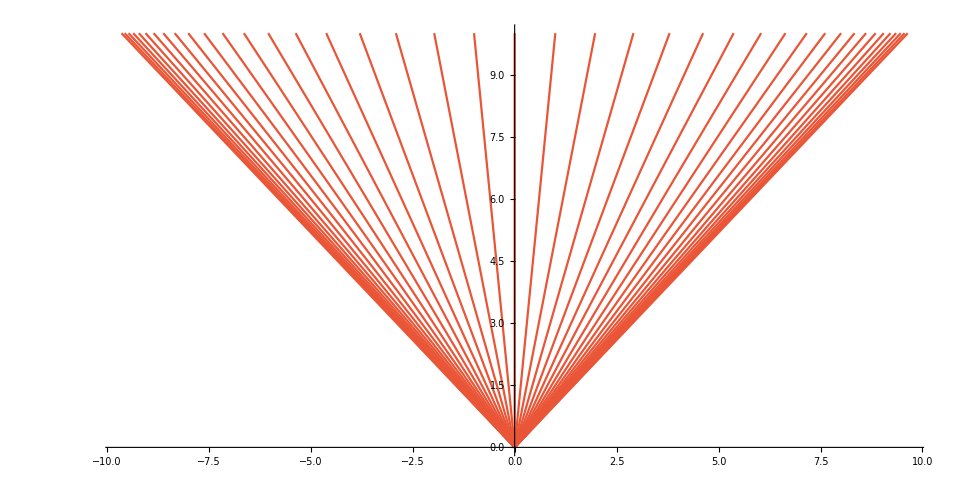

```mathematica
ParametricPlot[{curve},{t,0,10}]
```

### TraditionalForm

```mathematica
p1T/:
MakeBoxes[p1T,TraditionalForm]:=SubscriptBox["p","1⊥"];
p2T/:
MakeBoxes[p2T,TraditionalForm]:=SubscriptBox["p","2⊥"];
p3T/:
MakeBoxes[p3T,TraditionalForm]:=SubscriptBox["p","3⊥"];
pT/:
MakeBoxes[pT,TraditionalForm]:=SubscriptBox["p","⊥"];
p23T/:
MakeBoxes[p23T,TraditionalForm]:=SubscriptBox["p","23⊥"];
τZ/:
MakeBoxes[τZ,TraditionalForm]:=SubscriptBox["τ","Z"];
τXZ/:
MakeBoxes[τXZ,TraditionalForm]:=SubscriptBox["τ","X-Z"];
```

## Gain term

```mathematica
$PrePrint=StandardForm;
```

#### Try two first

```mathematica
Quit[]
```

```mathematica
η1ηZ={pT E^η+p1T eη1-p23T eηZ,pT E^-η+p1T/eη1-p23T/eηZ}
```

{eη1 p1T-eηZ p23T+ⅇ^η pT,p1T/eη1-p23T/eηZ+ⅇ^-η pT}

```mathematica
jacob=Det[Table[D[η1ηZ[[i]],eη[[j]]],{i,1,2},{j,1,2}]]
```

-(p1T p23T)/eη1^2+(p1T p23T)/eηZ^2

```mathematica
sol1Z=FullSimplify[Solve[η1ηZ==0,{eη1,eηZ}],η∈Reals]
```

{{eη1→-(ⅇ^η (p1T^2-p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2+pT^2-√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p23T pT)},{eη1→(ⅇ^η (-p1T^2+p23T^2-pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p23T pT)}}

```mathematica
sol1Z={{eη1->-(ⅇ^η (p1T^2-p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p1T pT),eηZ->(ⅇ^η (-p1T^2+p23T^2+pT^2-√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p23T pT)},{eη1->(ⅇ^η (-p1T^2+p23T^2-pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p1T pT),eηZ->(ⅇ^η (-p1T^2+p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p23T pT)}};
```

```mathematica
sol1Z
```

{{eη1→-(ⅇ^η (p1T^2-p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2+pT^2-√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p23T pT)},{eη1→(ⅇ^η (-p1T^2+p23T^2-pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))))/(2 p23T pT)}}

```mathematica
FullSimplify[1/2(1/eηZ-eηZ)/.sol1Z/.{η->0}]
```

{(√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))/(2 p23T pT),-(√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))/(2 p23T pT)}

```mathematica
FullSimplify[(-p1T^2+p23T^2+pT^2)^2-(p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)]
```

4 p23T^2 pT^2

```mathematica
FullSimplify[eη1 eηZ jacob/.sol1Z,η∈Reals]
```

{-√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)),√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))}

```mathematica
condPC:={√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))->(𝒫^2)[pT,p1T,p23T]}
```

```mathematica
condPC//TraditionalForm
sol1Z/.{eη1->E^Subscript[η, 1],eηZ->E^Subscript[η, Z]}/.condPC//TraditionalForm
```

{√((p_(1⊥)-p_(23⊥)-p_⊥) (p_(1⊥)+p_(23⊥)-p_⊥) (p_(1⊥)-p_(23⊥)+p_⊥) (p_(1⊥)+p_(23⊥)+p_⊥))→𝒫^2(p_⊥,p_(1⊥),p_(23⊥))}

{{ⅇ^η_1→-(ⅇ^η (𝒫^2(p_⊥,p_(1⊥),p_(23⊥))+p_(1⊥)^2-p_(23⊥)^2+p_⊥^2))/(2 p_(1⊥) p_⊥),ⅇ^η_Z→(ⅇ^η (-𝒫^2(p_⊥,p_(1⊥),p_(23⊥))-p_(1⊥)^2+p_(23⊥)^2+p_⊥^2))/(2 p_(23⊥) p_⊥)},{ⅇ^η_1→(ⅇ^η (𝒫^2(p_⊥,p_(1⊥),p_(23⊥))-p_(1⊥)^2+p_(23⊥)^2-p_⊥^2))/(2 p_(1⊥) p_⊥),ⅇ^η_Z→(ⅇ^η (𝒫^2(p_⊥,p_(1⊥),p_(23⊥))-p_(1⊥)^2+p_(23⊥)^2+p_⊥^2))/(2 p_(23⊥) p_⊥)}}

```mathematica
sol1Z=(sol1Z/.condPC)
```

{{eη1→-(ⅇ^η (p1T^2-p23T^2+PC+pT^2))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2-PC+pT^2))/(2 p23T pT)},{eη1→(ⅇ^η (-p1T^2+p23T^2+PC-pT^2))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2+PC+pT^2))/(2 p23T pT)}}

```mathematica
Jacob=(FullSimplify[eη1 eηZ jacob/.sol1Z,η∈Reals]/.condPC)
```

{-PC,PC}

#### Last one

```mathematica
FullSimplify[FullSimplify[ D[y-1/2 Log[(τ E^η- τZ eηZ)/(τ E^-η- τZ/eηZ)],τZ]/.{eηZ->E^ηZ}]- τ Sinh[ηZ-η]/((τ E^η- τZ eηZ) (τ E^-η- τZ/eηZ))/.{eηZ->E^ηZ}]
```

0

```mathematica
jacobτZ=FullSimplify[FullSimplify[D[y-1/2 Log[(τ E^η- τZ eηZ)/(τ E^-η- τZ/eηZ)],τZ]]/.sol1Z]
```

{(τ √((p_(1⊥)-p_(23⊥)-p_⊥) (p_(1⊥)+p_(23⊥)-p_⊥) (p_(1⊥)-p_(23⊥)+p_⊥) (p_(1⊥)+p_(23⊥)+p_⊥)))/(2 τ τZ (p_⊥^2-p_(1⊥)^2)-2 p_(23⊥) p_⊥ (τ^2+τZ^2)+2 τ τZ p_(23⊥)^2),-(τ √((p_(1⊥)-p_(23⊥)-p_⊥) (p_(1⊥)+p_(23⊥)-p_⊥) (p_(1⊥)-p_(23⊥)+p_⊥) (p_(1⊥)+p_(23⊥)+p_⊥)))/(2 τ τZ (p_⊥^2-p_(1⊥)^2)-2 p_(23⊥) p_⊥ (τ^2+τZ^2)+2 τ τZ p_(23⊥)^2)}

```mathematica
FullSimplify[Total[jacobτZ]]
```

0

```mathematica
solτZ=FullSimplify[Solve[Exp[2 y]-(τ E^η- τZ eηZ)/(τ E^-η- τZ/eηZ)==0, τZ]][[1]]
```

{τZ→(2 eηZ τ ⅇ^y sinh(y-η))/(ⅇ^(2 y)-eηZ^2)}

```mathematica
solτZ=FullSimplify[solτZ/.{eηZ->E^ηZ}]
```

{τ_Z→τ sinh(y-η) csch(y-ηZ)}

```mathematica
FullSimplify[Exp[y-η]-Sinh[y-η]/Sinh[y-ηZ] E^(y-ηZ)]
```

sinh(η-ηZ) csch(y-ηZ)

```mathematica
1/Csch[x]
```

sinh(x)

```mathematica
FullSimplify[jacobτZ/.solτZ]
```

{(√((p_(1⊥)-p_(23⊥)-p_⊥) (p_(1⊥)+p_(23⊥)-p_⊥) (p_(1⊥)-p_(23⊥)+p_⊥) (p_(1⊥)+p_(23⊥)+p_⊥)))/(2 τ (sinh(y-η) csch(y-ηZ) (-p_(1⊥)^2-p_(23⊥) p_⊥ sinh(y-η) csch(y-ηZ)+p_(23⊥)^2+p_⊥^2)-p_(23⊥) p_⊥)),-(√((p_(1⊥)-p_(23⊥)-p_⊥) (p_(1⊥)+p_(23⊥)-p_⊥) (p_(1⊥)-p_(23⊥)+p_⊥) (p_(1⊥)+p_(23⊥)+p_⊥)))/(2 τ (sinh(y-η) csch(y-ηZ) (-p_(1⊥)^2-p_(23⊥) p_⊥ sinh(y-η) csch(y-ηZ)+p_(23⊥)^2+p_⊥^2)-p_(23⊥) p_⊥))}

```mathematica
τXZ=FullSimplify[Sqrt[(τ E^η- τZ eηZ) (τ E^-η- τZ/eηZ)]/.sol1Z/.solτZ,τ>0]
```

{τ √((sinh(y-η) csch(y-ηZ) (p_(1⊥)^2+p_(23⊥) p_⊥ sinh(y-η) csch(y-ηZ)-p_(23⊥)^2-p_⊥^2))/(p_(23⊥) p_⊥)+1),τ √((sinh(y-η) csch(y-ηZ) (p_(1⊥)^2+p_(23⊥) p_⊥ sinh(y-η) csch(y-ηZ)-p_(23⊥)^2-p_⊥^2))/(p_(23⊥) p_⊥)+1)}

```mathematica
FullSimplify[τXZ[[1]]-τXZ[[2]]]
```

0

```mathematica
τXZ=τXZ[[1]]
```

τ √((sinh(y-η) csch(y-ηZ) (p_(1⊥)^2+p_(23⊥) p_⊥ sinh(y-η) csch(y-ηZ)-p_(23⊥)^2-p_⊥^2))/(p_(23⊥) p_⊥)+1)

```mathematica
Clear[τXZ]
```

```mathematica
coef=FullSimplify[1/(Abs[jacobτZ[[1]]] τZ τXZ/.solτZ/.condPC),τ>0&&(𝒫^2)[pT,p1T,p23T]>0]
```

(2 csch(y-η) sinh(y-ηZ) Abs[p_(23⊥) p_⊥+csch(y-ηZ) sinh(y-η) (p_(1⊥)^2-p_(23⊥)^2-p_⊥^2+p_(23⊥) p_⊥ csch(y-ηZ) sinh(y-η))])/(τ_(X-Z) 𝒫^2(p_⊥,p_(1⊥),p_(23⊥)))

```mathematica
coef//StandardForm
```

(2 Abs[p23T pT+Csch[y-ηZ] Sinh[y-η] (p1T^2-p23T^2-pT^2+p23T pT Csch[y-ηZ] Sinh[y-η])] Csch[y-η] Sinh[y-ηZ])/(τ √(1+(Csch[y-ηZ] Sinh[y-η] (p1T^2-p23T^2-pT^2+p23T pT Csch[y-ηZ] Sinh[y-η]))/(p23T pT)) 𝒫^2[pT,p1T,p23T])

```mathematica
coef=FullSimplify[1/(Abs[jacobτZ[[1]]] τZ τXZ/.solτZ/.condPC),τ>0&&(𝒫^2)[pT,p1T,p23T]>0&&Csch[y-ηZ] Sinh[y-η]>0]
```

(2 csch(y-η) sinh(y-ηZ) Abs[p_(23⊥) p_⊥+csch(y-ηZ) sinh(y-η) (p_(1⊥)^2-p_(23⊥)^2-p_⊥^2+p_(23⊥) p_⊥ csch(y-ηZ) sinh(y-η))])/(τ 𝒫^2(p_⊥,p_(1⊥),p_(23⊥)) √((sinh(y-η) csch(y-ηZ) (p_(1⊥)^2+p_(23⊥) p_⊥ sinh(y-η) csch(y-ηZ)-p_(23⊥)^2-p_⊥^2))/(p_(23⊥) p_⊥)+1))

```mathematica
condPC
```

{√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))→PC}

```mathematica
FullSimplify[√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))-]
```

#### Try 3 together

```mathematica
Quit[]
```

```mathematica
equation={pT E^y+p1T eη1-p23T eηZ,pT E^-y+p1T/eη1-p23T/eηZ,Exp[2 y]-(τ E^η- τZ eηZ)/(τ E^-η- τZ/eηZ)};
```

```mathematica
sol=FullSimplify[Solve[equation==0,{eη1,eηZ,τZ}]]
```

{{eη1→(-ⅇ^η p1T^2+ⅇ^η p23T^2-ⅇ^y pT^2+√(-4 ⅇ^(y+η) p23T^2 pT^2+(ⅇ^η (p1T-p23T) (p1T+p23T)-ⅇ^y pT^2)^2))/(2 p1T pT),eηZ→(-ⅇ^η p1T^2+ⅇ^η p23T^2+ⅇ^y pT^2+√(-4 ⅇ^(y+η) p23T^2 pT^2+(ⅇ^η (p1T-p23T) (p1T+p23T)-ⅇ^y pT^2)^2))/(2 p23T pT),τZ→(2 p23T pT τ)/(-p1T^2+p23T^2+(ⅇ^y (p1T^2-p23T^2+pT^2))/(ⅇ^y+ⅇ^η)+(√(ⅇ^(2 η) (p1T^2-p23T^2)^2-2 ⅇ^(y+η) (p1T^2+p23T^2) pT^2+ⅇ^(2 y) pT^4))/(-ⅇ^y+ⅇ^η))},{eη1→-(ⅇ^η (p1T-p23T) (p1T+p23T)+ⅇ^y pT^2+√(-4 ⅇ^(y+η) p23T^2 pT^2+(ⅇ^η (p1T-p23T) (p1T+p23T)-ⅇ^y pT^2)^2))/(2 p1T pT),eηZ→(-ⅇ^η p1T^2+ⅇ^η p23T^2+ⅇ^y pT^2-√(-4 ⅇ^(y+η) p23T^2 pT^2+(ⅇ^η (p1T-p23T) (p1T+p23T)-ⅇ^y pT^2)^2))/(2 p23T pT),τZ→(2 p23T pT τ)/(-p1T^2+p23T^2+(ⅇ^y (p1T^2-p23T^2+pT^2))/(ⅇ^y+ⅇ^η)+(√(ⅇ^(2 η) (p1T^2-p23T^2)^2-2 ⅇ^(y+η) (p1T^2+p23T^2) pT^2+ⅇ^(2 y) pT^4))/(ⅇ^y-ⅇ^η))}}

```mathematica
sol/.condPC
```

{{eη1→-(ⅇ^η (p1T^2-p23T^2+PC+pT^2))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2-PC+pT^2))/(2 p23T pT),τZ→(2 p23T pT τ Sinh[y-η] (PC Cosh[y-η]-(-p1T^2+p23T^2+pT^2) Sinh[y-η]))/(p1T^4+p23T^4+pT^4-2 p1T^2 (p23T^2+pT^2)-2 p23T^2 pT^2 Cosh[2 (y-η)])},{eη1→(ⅇ^η (-p1T^2+p23T^2+PC-pT^2))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2+PC+pT^2))/(2 p23T pT),τZ→-(2 p23T pT τ Sinh[y-η] (PC Cosh[y-η]+(-p1T^2+p23T^2+pT^2) Sinh[y-η]))/(p1T^4+p23T^4+pT^4-2 p1T^2 (p23T^2+pT^2)-2 p23T^2 pT^2 Cosh[2 (y-η)])}}

```mathematica
FullSimplify[(eηZ E^-η-τZ/τ)/.sol/.condPC]
```

{(-p1T^2+p23T^2-PC+pT^2)/(2 p23T pT)+(2 p23T pT Sinh[y-η] (-PC Cosh[y-η]+(-p1T^2+p23T^2+pT^2) Sinh[y-η]))/(p1T^4+p23T^4+pT^4-2 p1T^2 (p23T^2+pT^2)-2 p23T^2 pT^2 Cosh[2 (y-η)]),(-p1T^2+p23T^2+PC+pT^2)/(2 p23T pT)+(2 p23T pT Sinh[y-η] (PC Cosh[y-η]+(-p1T^2+p23T^2+pT^2) Sinh[y-η]))/(p1T^4+p23T^4+pT^4-2 p1T^2 (p23T^2+pT^2)-2 p23T^2 pT^2 Cosh[2 (y-η)])}

```mathematica
FullSimplify[{{y->1/2+p1T^2/(2 p23T^2)+p1T^2/(2 pT^2)-p1T^4/(4 p23T^2 pT^2)-p23T^2/(4 pT^2)-pT^2/(4 p23T^2)+(√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))/(4 p23T^2)+(√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))/(4 pT^2)-(p1T^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))/(4 p23T^2 pT^2)+η}}]
```

{{y→1/(4 p23T^2 pT^2)(-p1T^4-p23T^4+p1T^2 (2 p23T^2+2 pT^2-√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))+pT^2 (-pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))+p23T^2 (√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))+pT^2 (2+4 η)))}}

```mathematica
solPC=FullSimplify[sol/.condPC/.{p1T^4+p23T^4+pT^4-2 p1T^2 (p23T^2+pT^2)-2 p23T^2 pT^2 Cosh[2 (y-η)]->PC^2-2 p23T^2 pT^2 (Cosh[2 (y-η)]-1)}]
```

{{eη1→-(ⅇ^η (p1T^2-p23T^2+PC+pT^2))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2-PC+pT^2))/(2 p23T pT),τZ→(2 p23T pT τ sinh(y-η) (PC cosh(y-η)-(-p1T^2+p23T^2+pT^2) sinh(y-η)))/(PC^2-4 p23T^2 pT^2 sinh^2(y-η))},{eη1→(ⅇ^η (-p1T^2+p23T^2+PC-pT^2))/(2 p1T pT),eηZ→(ⅇ^η (-p1T^2+p23T^2+PC+pT^2))/(2 p23T pT),τZ→-(2 p23T pT τ sinh(y-η) ((-p1T^2+p23T^2+pT^2) sinh(y-η)+PC cosh(y-η)))/(PC^2-4 p23T^2 pT^2 sinh^2(y-η))}}

```mathematica
FullSimplify[Sqrt[p1T^4+p23T^4+pT^4-2 p1T^2 (p23T^2+pT^2)-2 p23T^2 pT^2]]/.condPC
```

PC

```mathematica
eη={eη1,eηZ,τZ};
```

```mathematica
jacob=Det[Table[D[equation[[i]],eη[[j]]],{i,1,3},{j,1,3}]]
```

(ⅇ^η τ (eηZ^2-ⅇ^(2 η)) (eη1^2 p1T p23T-eηZ^2 p1T p23T))/(eη1^2 eηZ (ⅇ^η τZ-eηZ τ)^2)

```mathematica
FullSimplify[Sqrt[(τ E^η- τZ eηZ) (τ E^-η- τZ/eηZ)] /.solPC]
```

$Aborted

```mathematica
FullSimplify[eη1 eηZ τZ jacob/.solPC]
```

{(ⅇ^(2 η) sinh(y-η) (p1T^2-(p23T-pT)^2+PC) ((p1T+p23T) (p1T^2-p23T^2+PC)+pT^2 (p23T-p1T)) ((p1T-p23T) (p1T^2-p23T^2+PC)-pT^2 (p1T+p23T)) (-p1T^2+(p23T+pT)^2-PC) (2 p23T pT sinh(y-η)-PC) (2 p23T pT sinh(y-η)+PC) ((p1T^2-p23T^2-pT^2) sinh(y-η)+PC cosh(y-η)))/(PC^2 (p1T^2-p23T^2+PC+pT^2) (p1T^2 PC+p23T^2 (2 pT^2 (1-ⅇ^(2 η-2 y))-PC)+PC (PC-pT^2))^2),(ⅇ^(2 η) sinh(y-η) (-p1T^2+(p23T-pT)^2+PC) (pT^2 (p1T-p23T)-(p1T+p23T) (p1T^2-p23T^2-PC)) ((p1T-p23T) (p1T^2-p23T^2-PC)-pT^2 (p1T+p23T)) (-p1T^2+(p23T+pT)^2+PC) (-2 p23T pT sinh(y-η)-PC) (PC-2 p23T pT sinh(y-η)) ((-p1T^2+p23T^2+pT^2) sinh(y-η)+PC cosh(y-η)))/(PC^2 (-p1T^2+p23T^2+PC-pT^2) (p1T^2 (-PC)+p23T^2 (PC+2 pT^2 (1-ⅇ^(2 η-2 y)))+PC (PC+pT^2))^2)}

```mathematica
FullSimplify[Out[27][[1]] Out[28][[1]]]
```

(ⅇ^(2 η) sinh(y-η) (p1T^2-(p23T-pT)^2+PC) ((p1T+p23T) (p1T^2-p23T^2+PC)+pT^2 (p23T-p1T)) ((p1T-p23T) (p1T^2-p23T^2+PC)-pT^2 (p1T+p23T)) (-p1T^2+(p23T+pT)^2-PC) (2 p23T pT sinh(y-η)-PC) (2 p23T pT sinh(y-η)+PC) √((PC τ^2 (p1T^2 PC+p23T^2 (2 pT^2 (1-ⅇ^(2 η-2 y))-PC)+PC (PC-pT^2)) (PC (sinh(2 (y-η)) (p1T^2-p23T^2+PC-pT^2)+2 PC)+2 sinh^2(y-η) (-pT^2 (2 (p1T^2+p23T^2)+PC)+(p1T-p23T) (p1T+p23T) (p1T^2-p23T^2+PC)+pT^4)))/((p1T^2-p23T^2+PC-pT^2) (PC^2-4 p23T^2 pT^2 sinh^2(y-η))^2)) ((p1T^2-p23T^2-pT^2) sinh(y-η)+PC cosh(y-η)))/(√2 PC^2 (p1T^2-p23T^2+PC+pT^2) (p1T^2 PC+p23T^2 (2 pT^2 (1-ⅇ^(2 η-2 y))-PC)+PC (PC-pT^2))^2)

```mathematica
FullSimplify[Out[27][[2]] Out[28][[2]]]
```

(ⅇ^(2 η) sinh(y-η) (-p1T^2+(p23T-pT)^2+PC) (pT^2 (p1T-p23T)-(p1T+p23T) (p1T^2-p23T^2-PC)) ((p1T-p23T) (p1T^2-p23T^2-PC)-pT^2 (p1T+p23T)) (-p1T^2+(p23T+pT)^2+PC) (-2 p23T pT sinh(y-η)-PC) (PC-2 p23T pT sinh(y-η)) √((PC τ^2 (p1T^2 (-PC)+p23T^2 (PC+2 pT^2 (1-ⅇ^(2 η-2 y)))+PC (PC+pT^2)) (PC (sinh(2 (y-η)) (-p1T^2+p23T^2+PC+pT^2)+2 PC)+2 sinh^2(y-η) (pT^2 (PC-2 (p1T^2+p23T^2))+(p1T-p23T) (p1T+p23T) (p1T^2-p23T^2-PC)+pT^4)))/((-p1T^2+p23T^2+PC+pT^2) (PC^2-4 p23T^2 pT^2 sinh^2(y-η))^2)) ((-p1T^2+p23T^2+pT^2) sinh(y-η)+PC cosh(y-η)))/(√2 PC^2 (-p1T^2+p23T^2+PC-pT^2) (p1T^2 (-PC)+p23T^2 (PC+2 pT^2 (1-ⅇ^(2 η-2 y)))+PC (PC+pT^2))^2)

```mathematica
FullSimplify[Out[31]/.{PC->√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))}]
FullSimplify[Out[32]/.{PC->√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))}]
```

(ⅇ^(4 y+2 η) (p1T^2-(p23T-pT)^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (p1T^2-(p23T+pT)^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (p1T^3-p23T p1T^2-(p23T^2+pT^2) p1T+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) p1T-p23T (-p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))) (p1T^3+p23T p1T^2-(p23T^2+pT^2) p1T+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) p1T+p23T (-p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))) sinh(y-η) (√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))-2 p23T pT sinh(y-η)) (2 p23T pT sinh(y-η)+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) cosh(y-η)+(p1T^2-p23T^2-pT^2) sinh(y-η)) √((ⅇ^(-y-η) √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) (ⅇ^(2 y) (p1T^4+(-2 p23T^2-2 pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) p1T^2+p23T^4+pT^4-p23T^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))-pT^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))-2 ⅇ^(2 η) p23T^2 pT^2) τ^2 ((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT) cosh(y-η)+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) (p1T^2-p23T^2-pT^2) sinh(y-η)))/((p1T^2-p23T^2-pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (p1T^4-2 (p23T^2+pT^2) p1T^2+p23T^4+pT^4-2 p23T^2 pT^2 cosh(2 (y-η)))^2)))/((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT) (p1T^2-p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (ⅇ^(2 y) (p1T^4+(-2 p23T^2-2 pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) p1T^2+p23T^4+pT^4-p23T^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))-pT^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))-2 ⅇ^(2 η) p23T^2 pT^2)^2)

-((ⅇ^(4 y+2 η) (-p1T^2+(p23T-pT)^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (-p1T^2+(p23T+pT)^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (-p1T^3+p23T p1T^2+(p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) p1T-p23T (p23T^2-pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))) (-p1T^3-p23T p1T^2+(p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) p1T+p23T (p23T^2-pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))) sinh(y-η) (√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))-2 p23T pT sinh(y-η)) (2 p23T pT sinh(y-η)+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) cosh(y-η)+(-p1T^2+p23T^2+pT^2) sinh(y-η)) √((ⅇ^(-y-η) √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) (ⅇ^(2 y) (p1T^4-(2 p23T^2+2 pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) p1T^2+p23T^4+pT^4+p23T^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))+pT^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))-2 ⅇ^(2 η) p23T^2 pT^2) τ^2 ((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT) cosh(y-η)+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) (-p1T^2+p23T^2+pT^2) sinh(y-η)))/((-p1T^2+p23T^2+pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (p1T^4-2 (p23T^2+pT^2) p1T^2+p23T^4+pT^4-2 p23T^2 pT^2 cosh(2 (y-η)))^2)))/((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT) (p1T^2-p23T^2+pT^2-√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) (ⅇ^(2 y) (p1T^4-(2 p23T^2+2 pT^2+√((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))) p1T^2+p23T^4+pT^4+p23T^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))+pT^2 √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)))-2 ⅇ^(2 η) p23T^2 pT^2)^2))

```mathematica
FullSimplify[Series[Out[33],{y,η,1}]]
```

2 ⅇ^(2 η) √(τ^2) (y-η) √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT))+O((y-η)^2)

```mathematica
FullSimplify[Series[Out[34],{y,η,1}]]
```

-2 (ⅇ^(2 η) √((p1T-p23T-pT) (p1T+p23T-pT) (p1T-p23T+pT) (p1T+p23T+pT)) √(τ^2)) (y-η)+O[y-η]^2

```mathematica
η2η3={pT E^η+p2T eη2-p3T eη3,pT E^-η+p2T/eη2-p3T/eη3}
```

{eη2 p2T-eη3 p3T+ⅇ^η pT,p2T/eη2-p3T/eη3+ⅇ^-η pT}

```mathematica
FullSimplify[Solve[η2η3==0,{eη2,eη3}],η∈Reals]
```

{{eη2→-(ⅇ^η (p2T^2+√((p2T-p3T-pT) (p2T+p3T-pT) (p2T-p3T+pT) (p2T+p3T+pT))-p3T^2+pT^2))/(2 p2T pT),eη3→(ⅇ^η (-p2T^2-√((p2T-p3T-pT) (p2T+p3T-pT) (p2T-p3T+pT) (p2T+p3T+pT))+p3T^2+pT^2))/(2 p3T pT)},{eη2→(ⅇ^η (-p2T^2+√((p2T-p3T-pT) (p2T+p3T-pT) (p2T-p3T+pT) (p2T+p3T+pT))+p3T^2-pT^2))/(2 p2T pT),eη3→(ⅇ^η (-p2T^2+√((p2T-p3T-pT) (p2T+p3T-pT) (p2T-p3T+pT) (p2T+p3T+pT))+p3T^2+pT^2))/(2 p3T pT)}}

## Derivation of loss term

```mathematica
solz=Expand[FullSimplify[Solve[{Z==(z1+z3)/2,z12==z1-z2,z23==z2-z3},{z1,z2,z3}]]]
```

{{z1→Z+z12/2+z23/2,z2→Z-z12/2+z23/2,z3→Z-z12/2-z23/2}}

```mathematica
coor={(z1+z3)/2,z1-z2,z2-z3};
zd={z1,z2,z3};
```

```mathematica
FullSimplify[Det[Table[D[coor[[i]],zd[[j]]],{i,1,3},{j,1,3}]]]
```

1

```mathematica
Expand[FullSimplify[{(z1+z2)/2,(z3+z2)/2}/.solz]]
```

{{Z+z23/2,Z-z12/2}}

```mathematica
solz=Expand[FullSimplify[Solve[{Z==(z1+z2+z3)/3,z12==z1-z2,z13==z1-z3},{z1,z2,z3}]]]
```

{{z1→Z+z12/3+z13/3,z2→Z-(2 z12)/3+z13/3,z3→Z+z12/3-(2 z13)/3}}

```mathematica
y2y3={(pT+p1T)E^ηZ- p2T ey2-p3T ey3,(pT+p1T)E^-ηZ- p2T/ey2-p3T/ey3}
```

{-ey2 p2T-ey3 p3T+ⅇ^ηZ (p1T+pT),-p2T/ey2-p3T/ey3+ⅇ^-ηZ (p1T+pT)}

```mathematica
soly2y3=FullSimplify[Solve[y2y3==0,{ey2,ey3}],ηZ>0]
```

{{ey2→1/(2 p2T (p1T+pT))ⅇ^ηZ (p2T^2-p3T^2+(p1T+pT)^2+√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT))),ey3→1/(2 p3T (p1T+pT))ⅇ^ηZ (-p2T^2+p3T^2+(p1T+pT)^2-√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)))},{ey2→1/(2 p2T (p1T+pT))ⅇ^ηZ (p2T^2-p3T^2+(p1T+pT)^2-√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT))),ey3→1/(2 p3T (p1T+pT))ⅇ^ηZ (-p2T^2+p3T^2+(p1T+pT)^2+√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)))}}

```mathematica
y23={ey2,ey3};
```

```mathematica
J23=Det[Table[D[y2y3[[i]],y23[[j]]],{i,1,2},{j,1,2}]]
```

(p2T p3T)/ey2^2-(p2T p3T)/ey3^2

```mathematica
J23=FullSimplify[ey2 ey3 J23/.soly2y3]
```

{-√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)),√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT))}

```mathematica
Total[J23]
```

0

```mathematica
p23plus=FullSimplify[{p2T ey2,p3T ey3}/.soly2y3]
```

{{1/(2 (p1T+pT))ⅇ^ηZ (p2T^2-p3T^2+(p1T+pT)^2+√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT))),1/(2 (p1T+pT))ⅇ^ηZ (-p2T^2+p3T^2+(p1T+pT)^2-√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)))},{1/(2 (p1T+pT))ⅇ^ηZ (p2T^2-p3T^2+(p1T+pT)^2-√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT))),1/(2 (p1T+pT))ⅇ^ηZ (-p2T^2+p3T^2+(p1T+pT)^2+√((p1T-p2T-p3T+pT) (p1T+p2T-p3T+pT) (p1T-p2T+p3T+pT) (p1T+p2T+p3T+pT)))}}

```mathematica
FullSimplify[p23plus[[1,1]]-p23plus[[2,2]]]
```

(ⅇ^ηZ (p2T-p3T) (p2T+p3T))/(p1T+pT)

```mathematica
solpz=FullSimplify[Solve[Sqrt[pT^2+pz^2]+Sqrt[p1T^2+pz^2]==p2T+p3T,pz],p2T>0&&p3T>0]
```

{{pz→-(√((p1T-p2T-p3T-pT) (p1T+p2T+p3T-pT) (p1T-p2T-p3T+pT) (p1T+p2T+p3T+pT)))/(2 (p2T+p3T))},{pz→(√((p1T-p2T-p3T-pT) (p1T+p2T+p3T-pT) (p1T-p2T-p3T+pT) (p1T+p2T+p3T+pT)))/(2 (p2T+p3T))}}

```mathematica
Total[pz/.solpz]
```

0